# Motorbike net2 & net3

## Set Environment

```mathematica
home = "/home/lichao/scratch/pami/";workdir = "/home/lichao/git/geonb/";SetDirectory[workdir];
```

```mathematica
prefix = "quad_train_";suffix="_64";
```

```mathematica
Needs["Posecpp`","posecpp_network.wl"];
```

## Generate Network 2

### load raw data

```mathematica
rawData=LoadNetwork2Raw[home<>prefix<>"net2_raw"<>suffix<>".txt"];rawData//Dimensions
```

{318206,8}

### find best threshold

```mathematica
Module[{n = 500,v=2,a},a =ConstructNetwork2[rawData,n,v];Sow[Length[a]];
Complement[a,ConstructNetwork2[rawData,n,v-0.1]]]//Reap;
```

```mathematica
el2 = ConstructNetwork2[rawData,500,2];g2 = Graph[el2,VertexLabels->"Name"];
```

```mathematica
el2 = ConstructNetwork2[rawData,500,1.2];g2 = Graph[el2,VertexLabels->"Name"];
```

```mathematica
el2 = ConstructNetwork2[rawData,500,1.3];g2 = Graph[el2,VertexLabels->"Name"];(* for quad 64pix case*)
```

```mathematica
VertexCount[g2]
EdgeCount[g2]
```

199

1411

### Node Research

```mathematica
Part[VertexList[g2],Ordering[DegreeCentrality[g2],All,Greater]]
```

{592,608,623,744,240,446,312,735,564,691,85,90,768,558,715,797,772,536,347,742,94,132,565,251,201,701,631,527,404,250,295,791,383,109,71,133,72,279,157,612,286,268,759,426,148,416,369,47,567,514,478,303,55,252,569,82,40,475,516,402,158,393,189,63,37,92,282,621,67,466,297,333,579,367,229,410,719,76,774,594,490,315,262,644,535,206,136,89,389,9,541,790,603,171,664,16,507,321,294,628,156,755,651,414,233,14,457,264,241,36,2,705,613,771,582,625,220,578,17,690,679,515,745,451,423,276,729,551,198,197,153,635,118,105,20,682,661,575,746,555,552,543,642,439,406,365,336,357,655,632,191,353,152,145,140,112,311,761,35,756,680,600,780,724,670,611,591,559,713,432,430,549,352,337,317,289,273,248,654,318,210,202,188,186,185,182,177,159,126,123,640,86,66,58,57,53,44,39,22}

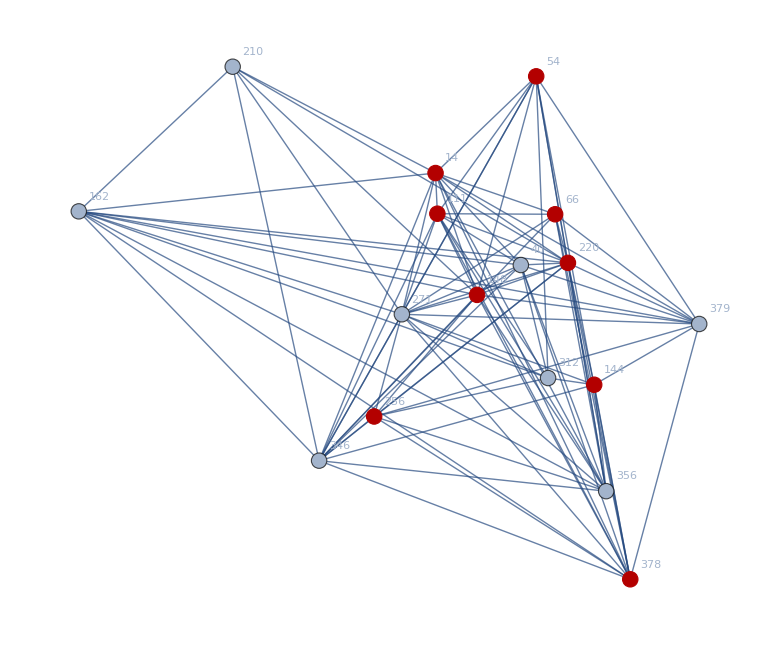

```mathematica
HighlightGraph[NeighborhoodGraph[g2,271,VertexLabels->"Name"],VertexList[g3]]
```

### Export Graph

```mathematica
Export[home<>prefix<>"net2_el"<>suffix<>".txt",EdgeList[g2]]
```

/home/lichao/scratch/pami/quad_train_net2_el_64.txt

## Load Network 3

### read Edge List

```mathematica
el3=LoadNetwork3[home<>prefix<>"net3_el_03_02"<>suffix<>".txt"]
```

{9<->416,14<->89,14<->579,16<->133,16<->426,20<->198,36<->63,36<->759,40<->478,47<->63,47<->759,55<->136,67<->297,72<->250,82<->286,82<->315,89<->475,89<->579,90<->251,90<->268,90<->536,92<->148,94<->312,94<->592,109<->402,132<->416,133<->279,133<->393,133<->426,133<->582,133<->631,148<->158,156<->241,157<->564,158<->294,171<->233,171<->567,171<->664,201<->251,201<->286,201<->369,201<->478,201<->701,206<->321,206<->333,206<->466,206<->594,233<->567,240<->768,251<->701,279<->393,279<->582,279<->631,295<->558,303<->628,312<->592,321<->594,367<->541,369<->631,369<->701,383<->475,383<->558,393<->426,393<->582,410<->565,416<->679,426<->582,446<->691,446<->768,451<->558,466<->594,475<->579,514<->772,527<->755,535<->594,558<->612,558<->631,558<->745,567<->664,567<->759,567<->772,569<->578,592<->608,592<->623,592<->735,621<->644,623<->691,691<->768,719<->744,759<->772}

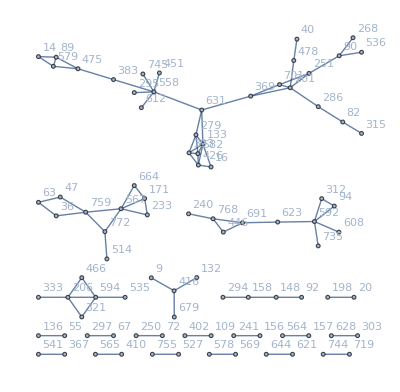

```mathematica
g3=Graph[el3,VertexLabels->"Name"]
```

```mathematica
VertexList[g3]//Sort//Length
```

87

```mathematica
comp3=ConnectedComponents[Graph[el3]]
```

{{295,558,383,451,612,631,745,475,133,279,369,89,579,16,393,426,582,201,701,14,251,286,478,90,82,40,268,536,315},{47,63,759,36,567,772,171,233,664,514},{240,768,446,691,623,592,94,312,608,735},{321,206,594,333,466,535},{294,158,148,92},{416,9,132,679},{156,241},{410,565},{628,303},{719,744},{55,136},{67,297},{569,578},{402,109},{250,72},{20,198},{621,644},{755,527},{157,564},{541,367}}

```mathematica
comp3//Length
```

20

## Load Global data

```mathematica
{gx,gy,gs,gn}=LoadGlobalData[home<>prefix<>"converge_x"<>suffix<>".txt",home<>prefix<>"converge_y"<>suffix<>".txt",home<>prefix<>"converge_s"<>suffix<>".txt",home<>prefix<>"converge_n"<>suffix<>".txt"];
```

```mathematica
cx = gx+gs/2;cy=-(gy+gs/2);
```

```mathematica
cx;
```

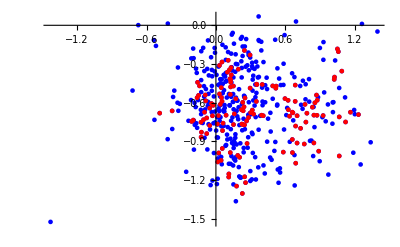

```mathematica
ListPlot[Map[{cx[#],cy[#]}&,{Keys[gx],VertexList[g3]},{2}],PlotStyle->{Blue,Red}]
```

```mathematica
Export[home<>prefix<>"global_summary"<>suffix<>".txt",Map[{#,gx[#],gy[#],gs[#]}&,Keys[gx]]]
```

/home/lichao/scratch/pami/quad_train_global_summary_64.txt

```mathematica
Intersection[#,Keys[gx]]&/@comp3
```

{{2,69,98,107,126,144,153,154,231,249,298,315,468,554},{1,32,109,118,212,225,311,347,364,365,370,485,538,597},{19,26,128,203,218,280,306,383,387,434,464,483,632},{51,81,239,267,290,327,406,508,636},{0,222,250,273,326,424,555},{155,209,300,312,534},{328,338,397,399,451},{410,446,593,642},{178,431,452},{93,214,512},{85,156,268},{137,200,232},{38,278,491},{174,179,474},{114,145,333},{258,292},{163,252},{65,284},{725,793},{24,83},{486,634},{111,167},{308,661},{566,635},{166,613},{321,360},{70,230},{402,498},{61,395},{62,187},{471,643},{14,349},{416,419}}

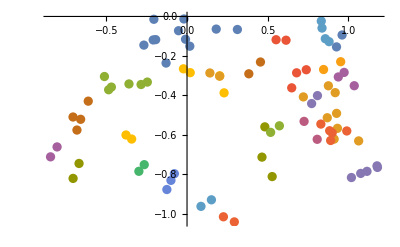

```mathematica
ListPlot[Map[{cx[#],cy[#]}&,Intersection[#,Keys[gx]]&/@comp3,{2}]]
```

```mathematica
ListPointPlot3D[Map[{cx[#],cy[#],gs[#]}&,Intersection[#,Keys[gx]]&/@comp3,{2}],Filling->Bottom,PlotStyle->PointSize[Large]]
```

-Graphics3D-

```mathematica
Mean[gs]
```

0.417891

```mathematica
StandardDeviation[gs]
```

0.130251

```mathematica
Mean/@Map[gs[#]&,Intersection[#,Keys[gx]]&/@comp3,{2}]
```

{0.360756,0.344439,0.362133,0.38136,0.352032,0.396469,0.767527,0.3965,0.372281,0.330848,0.836027,0.366872,0.475844,0.335979,0.410927,0.412599,0.766951,0.674244}

```mathematica
Map[gs[#]&,Intersection[#,Keys[gx]]&/@comp3,{2}]
```

{{0.354006,0.361811,0.358521,0.341208,0.368141,0.380846},{0.330545,0.34774,0.342344,0.362643,0.338923},{0.374262,0.34284,0.363975,0.367456},{0.381039,0.389704,0.373338},{0.346285,0.357779},{0.39348,0.399458},{0.813928,0.721127},{0.38905,0.403949},{0.376815,0.367747},{0.334944,0.326751},{0.755648,0.916406},{0.370876,0.362867},{0.456433,0.495254},{0.333575,0.338383},{0.412666,0.409188},{0.407534,0.417664},{0.837074,0.696827},{0.785451,0.563036}}

```mathematica
sOrderByD = gs[#]&/@Part[VertexList[g2],Ordering[DegreeCentrality[g2],All,Greater]];
```

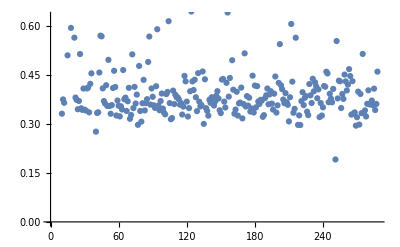

```mathematica
ListPlot[sOrderByD]
```

```mathematica
sOrderByP = gs[#]&/@Part[VertexList[g2],Ordering[PageRankCentrality[g2,0.1],All,Greater]];
```

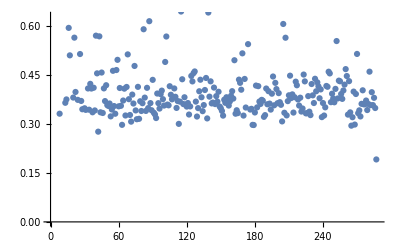

```mathematica
ListPlot[sOrderByP]
```

## Scale Slice

```mathematica
sLayers =SLayer[Keys[gx],gs]
```

<|6→{0,9,12,33,51,80,84,86,111,117,140,141,198,225,255,261,271,320,345,351,370},5→{2,7,14,20,22,23,31,35,36,37,40,49,54,57,61,63,64,66,69,77,82,85,89,90,94,103,112,121,124,126,136,138,139,142,145,153,154,158,160,161,163,165,166,167,169,171,174,176,177,179,184,187,191,193,195,197,199,202,203,204,206,208,209,213,216,222,224,227,234,236,243,246,252,256,257,263,267,269,281,283,284,285,291,293,295,296,297,298,300,301,302,304,306,307,309,313,318,322,327,330,334,335,338,340,352,354,361,364,365,368},4→{3,4,6,10,15,16,18,19,21,28,29,30,32,34,38,41,42,43,45,46,47,48,53,55,60,62,65,68,71,73,74,75,76,78,83,88,93,96,97,98,99,100,102,105,106,109,110,115,116,118,119,122,129,130,132,144,146,147,148,149,155,156,162,173,175,178,180,182,186,188,196,201,205,207,211,214,215,228,230,231,233,235,237,238,240,242,247,249,254,258,270,274,275,278,286,287,289,292,294,299,305,314,316,319,323,325,332,333,336,342,343,347,349,359,369,376},3→{5,24,52,67,92,107,133},8→{26,168,251,268,288,378,379,380,385},9→{56,72,128,135,328,344,356},7→{59,79,137,150,157,210,217,220,241,260,262,273,312,315,389},1→{218},10→{250,346}|>

```mathematica
ListPointPlot3D[Map[{cx[#],cy[#],gs[#]}&,Keys[gx]],Filling->Bottom,PlotStyle->PointSize[Large]]
```

-Graphics3D-

```mathematica
DeleteCases[Intersection[#,sLayers[4]]&/@comp3,{}]
```

{{93,119,211,242},{47,83,144,278,299},{130,148,376},{62,99},{292},{15,129},{238},{55,118}}

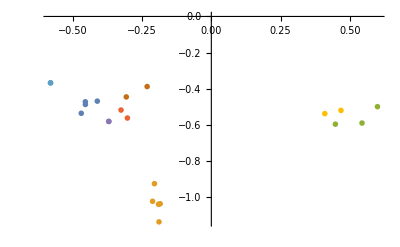

```mathematica
Module[{pos,idx},idx=DeleteCases[Intersection[#,sLayers[4]]&/@comp3,{}];pos=Map[{cx[#],cy[#]}&,idx,{2}];ListPlot[pos,PlotMarkers->idx]]
```

```mathematica
Export["ScaleLayer_"<>ToString[#]<>".pdf",SLayerPlot[#,sLayers,cx,cy]]&/@Keys[sLayers]
```

{ScaleLayer_6.pdf,ScaleLayer_5.pdf,ScaleLayer_4.pdf,ScaleLayer_3.pdf,ScaleLayer_8.pdf,ScaleLayer_9.pdf,ScaleLayer_7.pdf,ScaleLayer_1.pdf,ScaleLayer_10.pdf}

```mathematica
Directory
```

Directory

```mathematica
gall = Association[Map[#->{cx[#],cy[#],gs[#]}&,Keys[gx]]];
```

```mathematica
gall[0]
```

{0.111907,0.762903,0.476548}

```mathematica
SLayerPlot[1,sLayers,cx,cy]
```

SLayerPlot[1,<|6→{0,9,12,33,51,80,84,86,111,117,140,141,198,225,255,261,271,320,345,351,370},5→{2,7,14,20,22,23,31,35,36,37,40,49,54,57,61,63,64,66,69,77,82,85,89,90,94,103,112,121,124,126,136,138,139,142,145,153,154,158,160,161,163,165,166,167,169,171,174,176,177,179,184,187,191,193,195,197,199,202,203,204,206,208,209,213,216,222,224,227,234,236,243,246,252,256,257,263,267,269,281,283,284,285,291,293,295,296,297,298,300,301,302,304,306,307,309,313,318,322,327,330,334,335,338,340,352,354,361,364,365,368},4→{3,4,6,10,15,16,18,19,21,28,29,30,32,34,38,41,42,43,45,46,47,48,53,55,60,62,65,68,71,73,74,75,76,78,83,88,93,96,97,98,99,100,102,105,106,109,110,115,116,118,119,122,129,130,132,144,146,147,148,149,155,156,162,173,175,178,180,182,186,188,196,201,205,207,211,214,215,228,230,231,233,235,237,238,240,242,247,249,254,258,270,274,275,278,286,287,289,292,294,299,305,314,316,319,323,325,332,333,336,342,343,347,349,359,369,376},3→{5,24,52,67,92,107,133},8→{26,168,251,268,288,378,379,380,385},9→{56,72,128,135,328,344,356},7→{59,79,137,150,157,210,217,220,241,260,262,273,312,315,389},1→{218},10→{250,346}|>,cx,cy]

```mathematica
Manipulate[SLayerPlot[x,sLayers,cx,cy],{x,1,10,1}]
```

## Voronoi Centers for part

```mathematica
defined =Keys[gx];
```

```mathematica
voroComms= Intersection[defined,#]&/@Select[comp3,Length[#]>1&]
```

{{14,16,40,82,89,90,133,201,251,268,279,286,295,315,369,383,393,426,451,475,478,536,558,579,582,612,631,701,745},{36,47,63,171,233,514,567,664,759,772},{94,240,312,446,592,608,623,691,735,768},{206,321,333,466,535,594},{92,148,158,294},{9,132,416,679},{156,241},{410,565},{303,628},{719,744},{55,136},{67,297},{569,578},{109,402},{72,250},{20,198},{621,644},{527,755},{157,564},{367,541}}

```mathematica
centers =Mean/@Map[{gx[#],gy[#],Log[gs[#]]}&,voroComms,{2}]
```

{{0.838163,0.405751,-0.593856},{0.460031,0.597789,-0.694773},{0.0764685,0.122478,0.104004},{-0.808093,0.458987,-0.749862},{-0.143183,0.353339,-0.812478},{-0.294169,0.0190133,-0.61556},{-0.181351,0.826822,-0.680969},{0.408101,0.1391,-0.577937},{0.120703,0.99135,-0.671935},{-0.578704,0.581886,-0.194547},{-0.7074,0.292341,-0.824615},{-0.813008,0.523012,-0.417114},{-0.959185,0.303128,-0.389313},{-0.900089,0.781384,-0.376939},{0.278813,0.732781,-0.27802},{-0.248879,0.664556,-0.928512},{0.712497,0.828248,-0.548637},{0.204621,0.0290225,-0.549538},{-0.574893,0.37279,-0.030962},{-0.080843,1.03288,-0.809946}}

```mathematica
ListPointPlot3D[centers]
```

-Graphics3D-

```mathematica
Length[centers]
```

20

```mathematica
Export[home<>prefix<>"voro_centers"<>suffix<>".txt",centers]
```

/home/lichao/scratch/pami/quad_train_voro_centers_64.txt